# Hyperfine interaction

## Constant Declaration

```mathematica
e = 1.602176487 10^-19 C;
ℏ=1.054571628 10^-34 J s;
c=299792458 m s^-1;
me=9.10938215 10^-31 kg;
mn=1.67492729 10^-27 kg;
mp=1.672621637 10^-27 kg;
gp=5.585694713;
ge=-2.00231904622;
μ0=4 π 10^-7 kg/(m s^2);
ϵ0= 1/(μ0 c^2)//N;
```

```mathematica
(* composite constant *)
α=e^2/((4π ϵ0)ℏ c);
a=ℏ/(me c α);
μB= (e ℏ)/(2 me);
μN=(e ℏ)/(2mp);
μe=ge μB ;
μp=gp μN ;
γe=μe/(2π ℏ)
γp=μp/(2π ℏ)
```

-(2.8025×10^10 C)/kg

(4.25775×10^7 C)/kg

## the spinnor

```mathematica
S={(S1+S2)/2,(S1-S2)/(2ⅈ),S3};
II={(I1+I2)/2,(I1-I2)/(2ⅈ),I3};
S.II//Expand
```

(I2 S1)/2+(I1 S2)/2+I3 S3

```mathematica
μI=gp μN II/ℏ;
μS=ge μB S/ℏ;
```

## the magnetic dipole

```mathematica
r[1]=x;
r[2]=y;
r[3]=z;
```

```mathematica
T=Table[D[r[j]/((√(x^2+y^2+z^2))^3),r[i]],{i,1,3},{j,1,3}]
```

{{-(3 x^2)/((x^2+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(3/2)),-(3 x y)/((x^2+y^2+z^2)^(5/2)),-(3 x z)/((x^2+y^2+z^2)^(5/2))},{-(3 x y)/((x^2+y^2+z^2)^(5/2)),-(3 y^2)/((x^2+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(3/2)),-(3 y z)/((x^2+y^2+z^2)^(5/2))},{-(3 x z)/((x^2+y^2+z^2)^(5/2)),-(3 y z)/((x^2+y^2+z^2)^(5/2)),-(3 z^2)/((x^2+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(3/2))}}

```mathematica
B=μ0/(4π)(T.μI+μI KroneckerDelta[0,r]);
```

```mathematica
T.μI//Simplify//MatrixForm
```

(-(gp (6 I3 x z+I1 (2 x^2-3 ⅈ x y-y^2-z^2)+I2 (2 x^2+3 ⅈ x y-y^2-z^2)) μN)/(2 (x^2+y^2+z^2)^(5/2) ℏ)
-(ⅈ gp (-6 ⅈ I3 y z+I1 (x^2-3 ⅈ x y-2 y^2+z^2)-I2 (x^2+3 ⅈ x y-2 y^2+z^2)) μN)/(2 (x^2+y^2+z^2)^(5/2) ℏ)
(gp (-3 (I1 (x-ⅈ y)+I2 (x+ⅈ y)) z+2 I3 (x^2+y^2-2 z^2)) μN)/(2 (x^2+y^2+z^2)^(5/2) ℏ))

```mathematica
B[[1]]//Simplify//MatrixForm
```

(gp μ0 μN ((3 ⅈ (I1-I2) x y)/((x^2+y^2+z^2)^(5/2))-(6 I3 x z)/((x^2+y^2+z^2)^(5/2))-((I1+I2) (2 x^2-y^2-z^2))/((x^2+y^2+z^2)^(5/2))+(I1+I2) KroneckerDelta[0,r]))/(8 π ℏ)

```mathematica
μS[[1]]B[[1]]//Simplify//MatrixForm
```

1/(16 π ℏ^2)ge gp (S1+S2) μ0 μB μN ((3 ⅈ (I1-I2) x y)/((x^2+y^2+z^2)^(5/2))-(6 I3 x z)/((x^2+y^2+z^2)^(5/2))-((I1+I2) (2 x^2-y^2-z^2))/((x^2+y^2+z^2)^(5/2))+(I1+I2) KroneckerDelta[0,r])

## Hamiltonian

```mathematica
HSI=-Sum[μS[[i]]B[[i]],{i,1,3}]//Simplify
```

-1/(16 π (x^2+y^2+z^2)^(5/2) ℏ^2)ge gp μ0 μB μN (-I2 S1 x^2-3 I2 S2 x^2+4 I3 S3 x^2-6 ⅈ I2 S2 x y-I2 S1 y^2+3 I2 S2 y^2+4 I3 S3 y^2-6 I3 S1 x z-6 I3 S2 x z-6 I2 S3 x z+6 ⅈ I3 S1 y z-6 ⅈ I3 S2 y z-6 ⅈ I2 S3 y z+2 I2 S1 z^2-8 I3 S3 z^2-I1 (3 S1 (x-ⅈ y)^2+6 S3 (x-ⅈ y) z+S2 (x^2+y^2-2 z^2))+2 (I2 S1+I1 S2+2 I3 S3) (x^2+y^2+z^2)^(5/2) KroneckerDelta[0,r])

```mathematica
Collect[HSI, S3 I3]
```

-(ge gp I3 S3 μ0 μB μN (4 x^2+4 y^2-8 z^2+4 (x^2+y^2+z^2)^(5/2) KroneckerDelta[0,r]))/(16 π (x^2+y^2+z^2)^(5/2) ℏ^2)-1/(16 π (x^2+y^2+z^2)^(5/2) ℏ^2)ge gp μ0 μB μN (-I2 S1 x^2-3 I2 S2 x^2-6 ⅈ I2 S2 x y-I2 S1 y^2+3 I2 S2 y^2-6 I3 S1 x z-6 I3 S2 x z-6 I2 S3 x z+6 ⅈ I3 S1 y z-6 ⅈ I3 S2 y z-6 ⅈ I2 S3 y z+2 I2 S1 z^2-I1 (3 S1 (x-ⅈ y)^2+6 S3 (x-ⅈ y) z+S2 (x^2+y^2-2 z^2))+2 I2 S1 (x^2+y^2+z^2)^(5/2) KroneckerDelta[0,r]+2 I1 S2 (x^2+y^2+z^2)^(5/2) KroneckerDelta[0,r])

## Calculation

```mathematica
HF=-2/3 μ0 ge gp μB μN KroneckerDelta[0,l](S.II)/ℏ^2
```

```mathematica
HLI=-μ0/(2π) μB μN gp/r^3(L.II)/ℏ^2
HSI=μ0/(4π)ge μB gp μN 1/r^3 1/ℏ^2(S.II-3(S.r)(II.r))
```

```mathematica
S={(Sup+ Sdn)/2,(Sup-Sdn)/(2ⅈ),Sz}
II={(IIup+Sdn)/2,(Sup-Sdn)/(2ⅈ),Sz}
```

### The energy level

```mathematica
HLI[n_,J_,L_,I_]:=μ0 μB μN gp/(2π)1/a^3(J(J+1)-L(L+1)-I(I+1))/(n^3 L(L+1/2)(L+1))
HLI[2,3/2,1,1/2]-HLI[2,1/2,1,1/2]
```

```mathematica
(4.4140786028015696*^-26 C^8 kg^5 m^2)/(J^4 s^18)1/(ℏ 2π)
```

(6.66169×10^7 C^8 kg^5 m^2)/(J^5 s^19)

```mathematica
(4.4140786028015696*^-26 C^8 kg^5 m^2)/(J^4 s^18)
```

(6.66169×10^7 C^8 kg^5 m^2)/(J^5 s^19)

```mathematica
9.4276 10^-25/(4.4140786 10^-26)
```

21.358

```mathematica
1.4224/0.06662
```

21.3509

```mathematica
(* the magnetic moment *)
μev[m_]:=ge μB  1/ℏ S[m] 
μpv[m_]:=gp μN 1/ℏ Ip[m]
```

```mathematica
H=B/2{{-ω1,0,0,0},
{0,-ω2,0,0},
{0,0,ω2,0},
{0,0,0,ω1}}+
1/4{{ωF,0,0,0},
{0,-ωF,0,0},
{0,0,-ωF,0},
{0,0,0,ωF}}
```

{{-(B ω1)/2+ωF/4,0,0,0},{0,-(B ω2)/2-ωF/4,0,0},{0,0,(B ω2)/2-ωF/4,0},{0,0,0,(B ω1)/2+ωF/4}}

```mathematica
Eigensystem[H]//Simplify
```

{{1/4 (-2 B ω2-ωF),1/4 (2 B ω2-ωF),1/4 (-2 B ω1+ωF),1/4 (2 B ω1+ωF)},{{0,1,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}}}

```mathematica
1422.81/4/221
```

1.60951

```mathematica
Manipulate[Plot[{1/4 (-2 B ω1+ωF+4 A ωS),1/4 (2 B ω1+ωF+4 A ωS),-ωF/4+A ωS-1/2 √(B^2 ω2^2+4 b^2 ωS^2),-ωF/4+A ωS+1/2 √(B^2 ω2^2+4 b^2 ωS^2)},{B,0,0.1}],{ωS,0,711},{A,0,1},{b,0,4},{ωF,0,1422.81},{ω1,20000,27982},{ω2,20000,28067.6}]
```

```mathematica
Manipulate[Plot[{1/4 (-2 B ω1+ωF+A ωS),1/4 (2 B ω1+ωF+A ωS),1/4 (-ωF-A ωS-√(4 B^2 ω2^2+ωS^2)),1/4 (-ωF-A ωS+√(4 B^2 ω2^2+ωS^2))},{B,0,0.1}],{ωS,0,711},{A,0,1},{ωF,0,1422.81},{ω1,20000,27982},{ω2,20000,28067.6}]
```

```mathematica
Sz=ℏ/2{{1,0},{0,-1}};
Sx=ℏ/2{{0,1},{1,0}};
Sy=ℏ/2{{0,-ⅈ},{ⅈ,0}};
```

```mathematica
MatrixExp[-ⅈ/ℏ θ Sz]
```

{{ⅇ^(-(ⅈ θ)/2),0},{0,ⅇ^((ⅈ θ)/2)}}

```mathematica
Rx=MatrixExp[-ⅈ/ℏ θ Sx]
```

{{Cos[θ/2],-ⅈ Sin[θ/2]},{-ⅈ Sin[θ/2],Cos[θ/2]}}

```mathematica
Inverse[Rx].Sy.Rx//Simplify
```

{{-1/2 ℏ Sin[θ],-1/2 ⅈ ℏ Cos[θ]},{1/2 ⅈ ℏ Cos[θ],1/2 ℏ Sin[θ]}}

```mathematica
Inverse[Rx]//Simplify
```

{{Cos[θ/2],ⅈ Sin[θ/2]},{ⅈ Sin[θ/2],Cos[θ/2]}}

### New apprach

```mathematica
HF=A{{1,0,0,0},{0,-1,2,0},{0,2,-1,0},{0,0,0,1}};
MatrixForm[HF]
```

(A | 0 | 0 | 0
0 | -A | 2 A | 0
0 | 2 A | -A | 0
0 | 0 | 0 | A)

```mathematica
AA=μ0/(π a^3)2/3 ℏ^2 γe γp (4 π^2)1/4
```

-(2.3569×10^-25 C^8 kg^5 m^2)/(J^4 s^18)

```mathematica
Eigensystem[HF]
```

{{-3 A,A,A,A},{{0,-1,1,0},{0,0,0,1},{0,1,1,0},{1,0,0,0}}}

```mathematica
f=AA 4/(2π ℏ)
c/f
```

(1.42281×10^9)/(J s)

0.210705 J m

## Zeeman Effect

```mathematica
ω1=(ge μe-gp μp )kg/(C J s)
ω2=(ge μe+gp μp )kg/(C J s)
```

3.70245×10^-23

3.73397×10^-23

```mathematica
ω1/(2π ℏ)
```

(5.58771×10^10)/(J s)

```mathematica
HZ=B/2{{ω1,0,0,0},{0,ω2,0,0},{0,0,-ω2,0},{0,0,0,-ω1}}
```

{{(B ω1)/2,0,0,0},{0,(B ω2)/2,0,0},{0,0,-(B ω2)/2,0},{0,0,0,-(B ω1)/2}}

```mathematica
Clear[ω1,ω2]
```

```mathematica
Eigensystem[HF+HZ]//Expand
```

{{A-(B ω1)/2,A+(B ω1)/2,-A-1/2 √(16 A^2+B^2 ω2^2),-A+1/2 √(16 A^2+B^2 ω2^2)},{{0,0,0,1},{1,0,0,0},{0,(B ω2)/(4 A)-(√(16 A^2+B^2 ω2^2))/(4 A),1,0},{0,(B ω2)/(4 A)+(√(16 A^2+B^2 ω2^2))/(4 A),1,0}}}

```mathematica
AA=2.3569049754404656*^-25
```

2.3569×10^-25

```mathematica
AA/(2π ℏ)
```

```mathematica
(3.5570184829515654*^8)/(10^6 J s)
```

355.702/(J s)

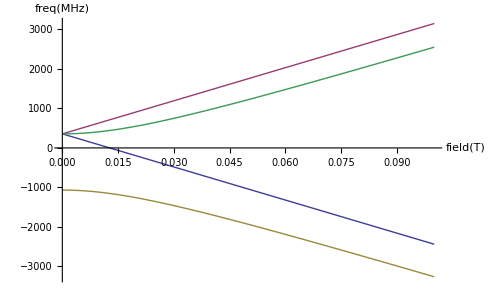

```mathematica
Plot[{1/2 (2 AA-B ω1) (J s)/(10^6 2π ℏ),(J s)/(10^6 2π ℏ)1/2 (2 AA+B ω1),(J s)/(10^6 2π ℏ)1/2 (-2 AA-√(16 AA^2+B^2 ω2^2)),1/(10^6 2) (-2 AA+√(16 AA^2+B^2 ω2^2))(J s)/(2π ℏ)},{B,0,0.1},AxesLabel->{field[T],freq [MHz]}]
```

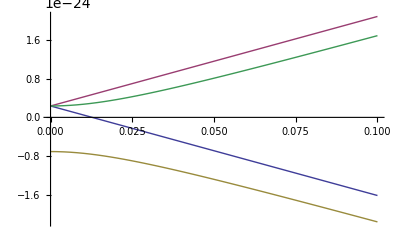

```mathematica
Plot[{1/2 (2 AA-B ω1) ,1/2 (2 AA+B ω1),1/2 (-2 AA-√(16 AA^2+B^2 ω2^2)),1/2 (-2 AA+√(16 AA^2+B^2 ω2^2))},{B,0,0.1}]
```